## Initial Stuff

```mathematica
SetDirectory[NotebookDirectory[]];
filelist = FileNames[All,"../plinear2"];
filenum =1;
```

### Useful functions

```mathematica
kBinslin[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(kmax-kmin)/(Nmax-1)//N;
result=Table[kmin +(i-1) Δ,{i,1,Nmax}];
result
];
```

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

### Plotting parameters and simple loop kernels

```mathematica
NmaxPlot=100;
NmaxFit=100;
kminPlot= 10^-3;
kminFit= 10^-3;
kmaxPlot=2.;
kmaxFit=0.6;
knPlot=kBins[NmaxPlot,kminPlot,kmaxPlot];
knFit=kBins[NmaxFit,kminFit,kmaxFit];
knFitlin=kBinslin[NmaxPlot,kminPlot,kmaxFit];
```

```mathematica
F3[q_,kmq_]=85/1512+(5 k^2)/(168 kmq^2)+kmq^2/(72 k^2)-(31 k^4)/(1512 q^4)-k^6/(252 kmq^2 q^4)+(11 k^2 kmq^2)/(252 q^4)-(5 kmq^4)/(504 q^4)-kmq^6/(108 k^2 q^4)-(5 k^2)/(1512 q^2)-k^4/(504 kmq^2 q^2)-(13 kmq^2)/(1512 q^2)+kmq^4/(72 k^2 q^2)-(7 q^2)/(216 k^2)-(19 q^2)/(504 kmq^2)+q^4/(72 k^2 kmq^2);
F3int=F3[√(qvec.qvec),√(kminq.kminq)]/.{kminq->k{0,0,1}-q{0,√(1-ν^2),ν},qvec->q{0,√(1-ν^2),ν}}//Simplify;

F2[q2_,kminq2_]=5/14+3(k^2/(28q2))+3(k^2/(28kminq2))-5(q2/(28kminq2))-5(kminq2/(28q2))+k^4/(14kminq2 q2);
F2int=F2[qvec.qvec,kminq.kminq]/.{kminq->k{0,0,1}-q{0,√(1-ν^2),ν},qvec->q{0,√(1-ν^2),ν}}//Simplify;
```

```mathematica
(*F3intν[ν_]=Integrate[F3int,ν];*)
```

```mathematica
(*F3intνval=F3intν[1]-F3intν[-1]//FullSimplify*)
```

```mathematica
(*F3intUVν=Normal[Series[F3intνval,{q,∞,2}]]*)
```

```mathematica
(*F3intUVsafe=F3intνval+(61 k^2)/(945 q^2)//Simplify;*)
```

### General Perturbation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m,k1,k2,k3];
Fn[n_,v_]:=Fn[n,v]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]:=Gn[n,v]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
```

```mathematica
F4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
sigma2[k1_,k2_]=1/4((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(mag[k1]^2 mag[k2]^2)-1;
```

```mathematica
Gal3[k1_,k2_,k3_]:=-1/2(1-3((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(4 mag[k1]^2 mag[k2]^2)+ ((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)(mag[k1+k3]^2-mag[k1]^2-mag[k3]^2)(mag[k3+k2]^2-mag[k3]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2 mag[k3]^2));
```

### Linear Power Spectrum (not IR re-summed)

```mathematica
plindat=ImportString[StringReplace[Import[(*filelist⟦58⟧*)filelist⟦1⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
kmin=plindat⟦1,1⟧;
kmax=Last[plindat]⟦1⟧;
```

```mathematica
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
(*pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.965},{i,1,30}];*)
```

```mathematica
(*plindat2=Join[pextra,plindat];*)
```

```mathematica
Clear[Plin]
Plin=Interpolation[plindat];
```

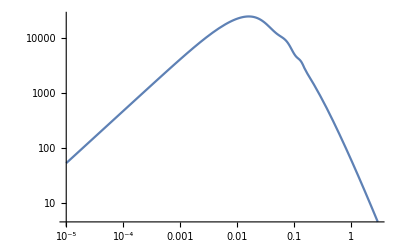

```mathematica
LogLogPlot[Plin[k],{k,kmin,3},PlotRange->Automatic]
```

### Linear Power Spectrum (IR re-summed)

#### Get non-re-summed power spectrum

```mathematica
SetDirectory[NotebookDirectory[]];
filelist = FileNames[All,"../plinear2"];
```

```mathematica
plindat=ImportString[StringReplace[Import[filelist⟦filenum⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
Plin=Interpolation[plindat];
```

```mathematica
Plin["Domain"]
```

{{0.00001,3.}}

#### Obtain Eisenstein-Hu PS

```mathematica
GetCosmoParam[paramstring_]:=Module[{Ωb,Ωc,h,ns},
(*Obtain cosmological parameters from first line in power spectrum .dat, assuming that the paramstring is for example:{"Ob0.05","Oc0.20","h0.62","ns1.10.dat"};*)

Ωb =ToExpression[StringSplit[paramstring⟦1⟧,"b"]⟦2⟧];Ωc= ToExpression[StringSplit[paramstring⟦2⟧,"c"]⟦2⟧];h =ToExpression[ StringSplit[paramstring⟦3⟧,"h"]⟦1⟧];ns = ToExpression[StringSplit[StringSplit[paramstring⟦4⟧,"s"]⟦2⟧,".dat"]⟦1⟧];
{Ωb,Ωc,h,ns}
]
```

```mathematica
GetEHuPS[k_,z_,Ωb_,Ωc_,h_,ns_]:=Module[{Ωm,logAs,Ho,ΩL,As,σ8,Tcmb,alph,ss,gamma,q,L0,C0,Tnw,Dlin,Dlinz,kP,PLnw},
(*Function that Outputs the E-Hu power spectrum pEH[k,z] for one cosmology;
Inputs:          ;
- k: scale;
- z: redshift;
- Ωb: baryon density parameter at z=0;
- Ωc: CDM density parameter at z=0;
- h: H0/(100 km/s/Mpc);
- ns: standard ns parameter;

Assumptions: flat universe, logAs=3.04, Tcmb=2.728;
*)

Ωm=Ωb+Ωc;ΩL=1-Ωm;

logAs = 3.04;Ho=1/2998 ;
As=(*2.21 10^-9*)10^-10 Exp[logAs];
σ8=0.8;Tcmb=2.728;
alph=1-0.328 Log[431 Ωm h^2] Ωb/Ωm+0.38 Log[22.3  Ωm h^2](Ωb/Ωm)^2;
ss=44.5 Log[9.83/(Ωm h^2)]/(√(1+10(Ωb h^2)^0.75))h;
gamma=Ωm h (alph+(1-alph)/(1+(0.43 ss k)^4));
q= (Tcmb/2.7)^2 k/gamma;
L0=Log[2 ⅇ+1.8 q];
C0=14.2+731/(1+62.5 q);
Tnw=L0/(L0+C0 q^2);
        Dlin[a_]:=-a/(3 √(Ωm (a^3 ΩL+Ωm))) (-8 Ωm Hypergeometric2F1[-1/2,5/6,11/6,-(a^3 ΩL)/Ωm]+(2 a^3 ΩL+5 Ωm) Hypergeometric2F1[1/2,5/6,11/6,-(a^3 ΩL)/Ωm]);
Dlinz=Dlin[1/(1+z)];
kP=0.05 h^-1;
2 π^2 4/25 (As k)/(Ho^4 Ωm^2)Dlinz^2(k/kP)^(ns-1)Tnw^2
]
```

```mathematica
paramstring = StringSplit[filelist⟦filenum⟧,"_"]⟦2;;⟧;
```

```mathematica
(*{Ωbo,Ωco,h,ns}=GetCosmoParam[paramstring];*)
Ωbo = 0.05;
Ωco = 0.26;
h = 0.68;
ns = 0.95;
```

```mathematica
PLnw[k_,z_]=GetEHuPS[k,z,Ωbo,Ωco,h,ns];
```

```mathematica
pEH=Table[{plindat⟦i,1⟧,PLnw[plindat⟦i,1⟧,0]},{i,1,Length[plindat]}];
```

```mathematica
(*ListLogLinearPlot[Transpose@{klin,plindat⟦All,2⟧/pEH⟦All,2⟧},Joined->True,PlotRange->{All,{0.935,1.065}},Frame->True,GridLines->{{}, {0.94,1.,1.06}}]*)
```

#### Smooth ratio and then multiply by the EH spectrum

```mathematica
Clear[f];
f[iR_,k_,λ_]:=NIntegrate[iR[10^x] PDF[NormalDistribution[Log10[k],λ]][x],{x,Log10[k]-4 λ,Log10[k]+4 λ},WorkingPrecision->10]
```

```mathematica
ExtractWiggle[plindat_,psmoothdat_]:=Module[{iR,λ,pnw,pw,ipnw,ipw,ktab},
λ=0.25;

ktab=plindat⟦All,1⟧;
iR=Interpolation[Transpose@{ktab,plindat⟦All,2⟧/psmoothdat⟦All,2⟧}];

pnw=Table[{ktab⟦i⟧,psmoothdat⟦i,2⟧ f[iR,ktab⟦i⟧,λ]},{i,1,Length[ktab]}];
pw=Table[{ktab⟦i⟧,plindat⟦i,2⟧-pnw⟦i,2⟧},{i,1,Length[ktab]}];
ipnw=Interpolation[pnw];
ipw=Interpolation[pw];

{ipnw,ipw}
]
```

```mathematica
GetΣtot2[psmooth_,f_]:=Module[{Σ2,δΣ2,Σtot2,losc=110,kmin},
kmin=psmooth["Domain"]⟦1,1⟧;
Σ2=1/(6 π^2)NIntegrate[(1-SphericalBesselJ[0,q losc]+2 SphericalBesselJ[2,q losc])psmooth[q],{q,kmin,0.2}];δΣ2=1/(2 π^2)NIntegrate[SphericalBesselJ[2,q losc]psmooth[q],{q,kmin,0.2}];Σtot2=(1+f 1/3(2+f))Σ2+f^2(-2/15)δΣ2
]
ResumPSNLO[k_,psmooth_,pwiggle_,Σtot2_]:=psmooth[k]+(1+k^2 Σtot2) Exp[-k^2 Σtot2]pwiggle[k] (*Next to leading order resummation*);
ResumPSLO[k_,psmooth_,pwiggle_,Σtot2_]:=psmooth[k]+ Exp[-k^2 Σtot2]pwiggle[k] (*Leading order resummation*);
```

```mathematica
{ipnw,ipw}=ExtractWiggle[plindat,pEH];
```

```mathematica
Σtot2=GetΣtot2[ipnw,0.6];
```

```mathematica
presLO[k_,f_]:=ResumPSLO[k,ipnw,ipw,Σtot2];
presNLO[k_,f_]:=ResumPSNLO[k,ipnw,ipw,Σtot2];
```

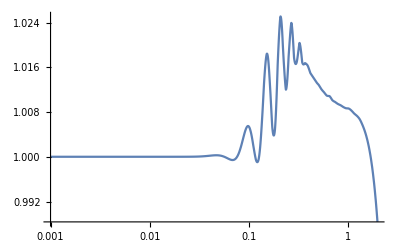

```mathematica
LogLinearPlot[presNLO[k,0.6]/Plin[k],{k,0.001,2},PlotRange->All]
```

## Fit broadband power spectrum

```mathematica
imax=3;
```

### Fit integer powers to linear power spectrum - linear fit with fixed parameters

```mathematica
Pirres[k_]=presNLO[k,0.6];
(*Plin[k_]=presNLO[k,0.6];*)
```

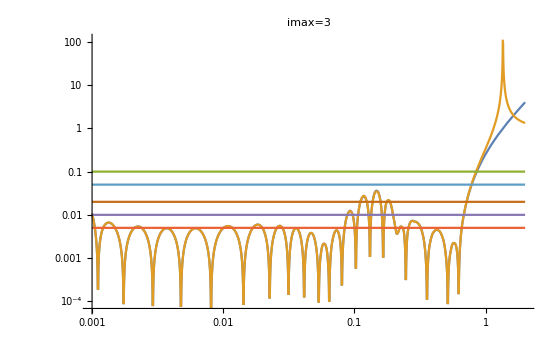

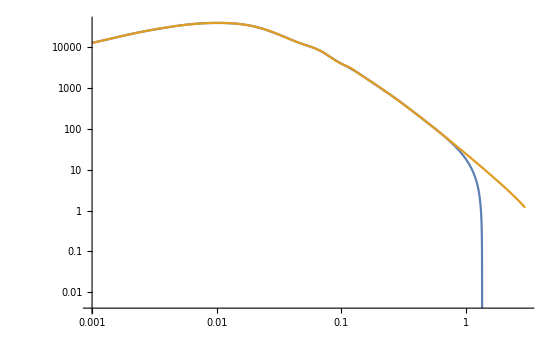

{-22.4831,1560.35,82085.3,-80957.,-248.435,7586.46,-76979.,46615.3,1883.5,-19988.7,-9348.3,352636.,-3303.03,28830.9,46163.,-1.01774×10^6}

```mathematica
ibias=0;
Clear[kuv,parametersconstraint,Psmoothtab,MyPsmoothtab,errors,kuv1,kuv2,kuv3,nlm,MyFitFunctions,Pinteger];
Psmoothtab = Table[{knFit⟦i⟧,Pirres[knFit⟦i⟧]},{i,1,Length[knFit]}];
MyPsmoothtab=Table[{Psmoothtab⟦i,1⟧,Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧},{i,1,Length[knFit]}];
errors=Flatten[Table[{Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];

imax=3;

ClearAll[kuv1,kuv2,kuv3,kpeak1,kpeak2,kpeak3,nlm,Pinteger]

(*Henry new params;*)

kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=(*0.006*)-0.001;
kpeak3=(*0.000076*)-0.000076;
kpeak4=-0.0000156;


Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];
MyFitFunctions=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k]/k^ibias;
(*Pintegerinterp=FunctionInterpolation[Pinteger[k],{k,0.0001,10}];*)
LogLogPlot[{Abs[Pinteger[k]/Pirres[k]-1],Abs[Pirres[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]
LogLogPlot[{Pinteger[k],Pirres[k]},{k,0.001,3},PlotRange->All]
MyPWiggle[k_]=Pirres[k]-Pinteger[k];
coefnowig=nlm["BestFitParameters"]
```

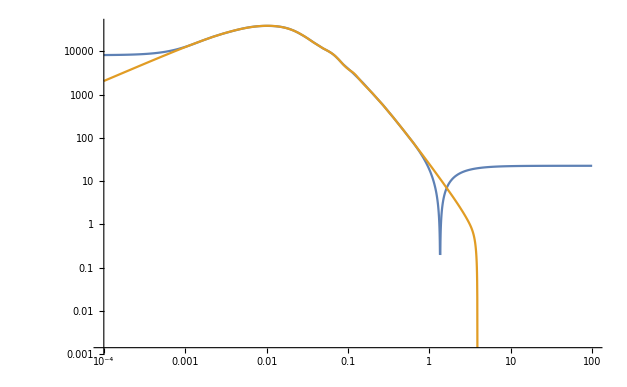

```mathematica
LogLogPlot[{Evaluate@Abs@{Pinteger[k]},Pirres[k]},{k,0.0001,100},PlotRange->All]
```

## 1-loop power-spectrum - constructing tables of exponents and coefficients from kernels

```mathematica
ktab= {0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3(*,0.4,0.5,0.6,0.7,0.8,0.9,1.0*)};
```

```mathematica
subsp1loop={kmq-> √(q^2+k^2-2 k q ν),kpq-> √(q^2+k^2+2 k q ν)};
```

### Calculate P22

#### P22 tables

```mathematica
(*CTab22full has the form {n1,n2,n3,#} where n1 = Exponent[q^2], n2 = Exponent[(k-q)^2]*)
```

```mathematica
Clear[q,k,Tab22,CTab22full]
ker22 = (2F2s[q,k-q]F2s[q,k-q]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq}//Expand);
ker22list=(List@@ker22);
```

#### Numerical check

```mathematica
ker22simple=ker22/.{kmq-> √(q^2+k^2-2 k q ν)}//Simplify;
```

```mathematica
P22damped[ks_]:=2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Pirres[√(q^2+k^2-2 k q ν)/.k->ks]Pirres[q]/.{k->ks},{q,10^-3,1},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->15,WorkingPrecision->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0}])
```

212.000410832166

```mathematica
P22exact[ks_]:=2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Plin[√(q^2+k^2-2 k q ν)/.{k->ks}]Plin[q](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{k->ks},{q,10^-3,1},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->12])
```

211.981

```mathematica
P22fit[ks_]:=2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Pinteger[√(q^2+k^2-2 k q ν)/.{k->ks}]Pinteger[q](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{k->ks},{q,10^-3,1},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->12])
```

### Calculate P13

#### P13 tables

```mathematica
ker13= (6F3s[q,-q,k]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq,mag[0]->0}//Expand);
(*ker13diogoUVν=Normal[Series[ker13diogo/.subsp1loop,{q,∞,2}]];
ker13diogoUV=Integrate[ker13diogoUVν,{ν,-1,1}]/2;*)
ker13UV=-(61 k^2)/(315 q^2);
ker13UVsafe=(ker13/.{kpq->kmq})-ker13UV;
```

#### Numerical Check of P13

```mathematica
ker13q=Integrate[ker13/.{kmq-> √(q^2+k^2-2 k q ν)},{ν,-1,1},Assumptions->{q>0,k>0}];
```

```mathematica
P13exact[ks_]:=2π (1/(π)^(3/2))Plin[ks](NIntegrate[q^2(ker13q Plin[q])/.k->ks,{q,10^-3,1},Method->{"GlobalAdaptive"},PrecisionGoal->30,WorkingPrecision->40])
```

100.724 NIntegrate[q^2 (ker13q pylinwig[q])/.k→0.8,{q,0.00001,15},Method→{GlobalAdaptive},PrecisionGoal→30,WorkingPrecision→40]

```mathematica
P13fit[ks_]:=2π (1/(π)^(3/2))Plin[ks](NIntegrate[q^2(ker13q Pinteger[q])/.k->ks,{q,10^-3,1},Method->{"GlobalAdaptive"},PrecisionGoal->30,WorkingPrecision->40])
```

```mathematica
P13damped[ks_]:=2π (1/(π)^(3/2))Plin[ks](NIntegrate[q^2(ker13q Pirres[q])/.k->ks,{q,10^-3,1},Method->{"GlobalAdaptive"},PrecisionGoal->30,WorkingPrecision->40])
```

100.724 NIntegrate[q^2 (ker13q Plin[q])/.k→0.8,{q,0.0001,3},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]

### Compute full P1-loop

```mathematica
p22numinttab = Table[{ktab⟦i⟧,P22fit[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

```mathematica
p13numinttab = Table[{ktab⟦i⟧,P13fit[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

```mathematica
p1loopnuminttab = Table[{ktab⟦i⟧,p22numinttab⟦i,2⟧ + p13numinttab⟦i,2⟧},{i,1,Length[ktab]}]
```

{{0.01,213.91012958209965317+24261.7 NIntegrate[q^2 (ker13q pylin[q])/.k→0.01,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.02,2159.0430075421713845+25259.8 NIntegrate[q^2 (ker13q pylin[q])/.k→0.02,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.03,6660.2763662207256241+19999.4 NIntegrate[q^2 (ker13q pylin[q])/.k→0.03,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.04,12714.254631086581459+15015.1 NIntegrate[q^2 (ker13q pylin[q])/.k→0.04,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.05,19385.500578287145727+12043.2 NIntegrate[q^2 (ker13q pylin[q])/.k→0.05,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.1,53947.175098525714744+5160.24 NIntegrate[q^2 (ker13q pylin[q])/.k→0.1,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.2,89151.615791588791958+1805.69 NIntegrate[q^2 (ker13q pylin[q])/.k→0.2,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.3,99685.632699250742252+804.832 NIntegrate[q^2 (ker13q pylin[q])/.k→0.3,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]}}

```mathematica
p1loopnumtab = Table[{ktab⟦i⟧,P22exact[ktab⟦i⟧]+P13exact[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

$Aborted

```mathematica
p1looprat = Table[{ktab⟦i⟧,Abs[(p1loopnuminttab⟦i,2⟧-p1loopnumtab⟦i,2⟧)/ p1loopnumtab⟦i,2⟧]},{i,1,Length[ktab]}]
```

{{0.1,0.00107513},{0.2,0.00939089},{0.3,0.00631535},{0.4,0.0103051},{0.5,0.0063505},{0.6,0.000514346},{0.7,0.000720304},{0.8,0.0030615},{0.9,0.00720093},{1.,0.0098753}}

{{0.1,1.08574×10^-6},{0.2,7.26971×10^-7},{0.3,2.07973×10^-6},{0.4,2.36092×10^-6},{0.5,1.90878×10^-6},{0.6,9.09179×10^-8},{0.7,1.30721×10^-6},{0.8,3.96975×10^-7},{0.9,2.20066×10^-6},{1.,0.0000121315}}